```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
Get[dddRicardo]
eme=4;
ege=3;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400(*,{3,4}*)},(*FinalCosts=*){{eme*ege,U1}/.U1->0(*,{8,0}*)},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@Data2Equations[Data];
(rulesgrid = CriticalCongestionSolver[d2egrid];)//AbsoluteTiming
```

MFGSS: {True,jt1≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt15≥0&&jt18≥0&&jt20≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt28≥0&&jt29≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&182000+2415 jt11+2415 jt12+2415 jt34≤2415 jt23+2415 jt24+2415 jt28+2415 jt29&&jt38≥0&&jt40≥0&&jt41≥0&&jt45≥0&&jt46≥0&&jt47≥0&&jt48≥0&&140000+2415 jt1+2415 jt10+2415 jt18+2415 jt46≤2415 jt11+2415 jt15+2415 jt33+2415 jt34+2415 jt35+2415 jt40+2415 jt41&&jt50≥0&&jt52≥0&&jt54≥0&&115 jt20+115 jt54≥12000+115 jt45+115 jt46+115 jt47&&196000+2415 jt20≤2415 jt45+2415 jt46+2415 jt47+2415 jt52&&jt58≥0&&jt60≥0&&jt63≥0&&2000+115 jt11+115 jt12+115 jt34+115 jt58+115 jt60≥115 jt23+115 jt24+115 jt28+115 jt29+115 jt36+115 jt38&&jt66≥0&&jt68≥0&&518000+2415 jt1+2415 jt10+2415 jt12+2415 jt18+2415 jt46+2415 jt58+2415 jt60+2415 jt63≤2415 jt15+2415 jt23+2415 jt24+2415 jt28+2415 jt29+2415 jt33+2415 jt35+2415 jt36+2415 jt38+2415 jt40+2415 jt41+2415 jt48+2415 jt50+2415 jt68&&69 u1≤48400&&jt1+jt10≥jt11+jt15&&5 jt1+5 jt10+5 jt12+5 jt18+5 jt46+5 jt58+5 jt60+5 jt63+5 jt66≥5 jt15+5 jt23+5 jt24+5 jt28+5 jt29+5 jt33+5 jt35+5 jt36+5 jt38+5 jt40+5 jt41+5 jt48+5 jt50&&jt1≥jt11&&jt15≤jt20&&jt11+jt12≥jt33+jt36&&182000+2415 jt11+2415 jt12≥2415 jt28+2415 jt29&&182000+2415 jt11+2415 jt12≥2415 jt10&&jt1+jt10+jt18≥jt11+jt15+jt45+jt48&&140000+2415 jt1+2415 jt10+2415 jt18≥2415 jt11+2415 jt15+2415 jt40+2415 jt41&&140000+2415 jt1+2415 jt10+2415 jt18≥2415 jt11+2415 jt20&&115 jt54≤12000+115 jt45+115 jt46+115 jt47&&115 jt40+115 jt50≤12000+115 jt45+115 jt46+115 jt47&&196000+2415 jt20≥2415 jt52&&196000+2415 jt20≥2415 jt18&&22400+161 jt1+161 jt10≥161 jt11+161 jt12&&jt25≤jt58&&182000+2415 jt11+2415 jt12+2415 jt34+2415 jt63≤2415 jt23+2415 jt24+2415 jt28+2415 jt29+2415 jt36+2415 jt38&&2000+115 jt11+115 jt12+115 jt34+115 jt60≤115 jt23+115 jt24+115 jt28+115 jt29+115 jt36+115 jt38&&2000+115 jt11+115 jt12+115 jt34+115 jt35≤115 jt23+115 jt24+115 jt28+115 jt36+115 jt38&&126000+805 jt11+805 jt12+805 jt34+805 jt58+805 jt60+805 jt63≥805 jt23+805 jt24+805 jt28+805 jt29+805 jt36+805 jt38+805 jt68&&126000+805 jt11+805 jt12+805 jt34+805 jt58+805 jt63≥805 jt23+805 jt24+805 jt28+805 jt29+805 jt36+805 jt38&&2415 jt24≤196000+2415 jt58&&115 jt1+115 jt10+115 jt18+115 jt46+115 jt66≤2000+115 jt11+115 jt15+115 jt33+115 jt34+115 jt35+115 jt40+115 jt41+115 jt48+115 jt50&&115 jt58≤12000+115 jt23+115 jt24+115 jt25&&0≤12000+115 jt23+115 jt24&&23 jt28+23 jt38≤2800+23 jt33+23 jt34+23 jt35&&115 jt1+115 jt10+115 jt18+115 jt46+115 jt47≤2000+115 jt11+115 jt15+115 jt33+115 jt34+115 jt35+115 jt40+115 jt48+115 jt50&&-518000≤2415 jt1-2415 jt23-2415 jt25≤448000&&-448000≤-2415 jt52-2415 jt54+2415 jt66+2415 jt68≤518000&&u1≥u37,(jt1==0||518000+2415 jt1==0)&&(jt23+jt25==0||0==448000+2415 jt23+2415 jt25)&&(jt1+jt10==jt11||22400+161 jt1+161 jt10==161 jt11)&&(jt11+jt12==0||182000+2415 jt11+2415 jt12==0)&&(jt20==0||196000+2415 jt20==0)&&(jt1+jt10+jt18==jt11+jt15||140000+2415 jt1+2415 jt10+2415 jt18==2415 jt11+2415 jt15)&&(jt20==0||196000+2415 jt20==0)&&(jt23+jt24==0||0==12000+115 jt23+115 jt24)&&(jt58==0||0==196000+2415 jt58)&&(jt33+jt34+jt35==0||0==2800+23 jt33+23 jt34+23 jt35)&&(182000+2415 jt11+2415 jt12+2415 jt34==2415 jt23+2415 jt24+2415 jt28+2415 jt29+2415 jt36+2415 jt38||2000+115 jt11+115 jt12+115 jt34==115 jt23+115 jt24+115 jt28+115 jt29+115 jt36+115 jt38)&&(jt45+jt46+jt47==0||0==12000+115 jt45+115 jt46+115 jt47)&&(140000+2415 jt1+2415 jt10+2415 jt18+2415 jt46==2415 jt11+2415 jt15+2415 jt33+2415 jt34+2415 jt35+2415 jt40+2415 jt41+2415 jt48+2415 jt50||115 jt1+115 jt10+115 jt18+115 jt46==2000+115 jt11+115 jt15+115 jt33+115 jt34+115 jt35+115 jt40+115 jt41+115 jt48+115 jt50)&&(448000==2415 jt52+2415 jt54||jt52+jt54==0)&&(jt58==0||0==196000+2415 jt58)&&(2000+115 jt11+115 jt12+115 jt34+115 jt58+115 jt60+115 jt63==115 jt23+115 jt24+115 jt28+115 jt29+115 jt36+115 jt38||126000+805 jt11+805 jt12+805 jt34+805 jt58+805 jt60+805 jt63==805 jt23+805 jt24+805 jt28+805 jt29+805 jt36+805 jt38)&&(2415 jt66+2415 jt68==518000||jt66+jt68==0)&&(jt1==0||jt23+jt25==0)&&(jt10==0||jt12==0)&&(jt11==0||182000+2415 jt11+2415 jt12==2415 jt10)&&(196000+2415 jt20==2415 jt18||jt15==0)&&(140000+2415 jt1+2415 jt10+2415 jt18==2415 jt11+2415 jt20||jt1+jt10==jt11+jt15)&&(jt15==jt20||jt18==0)&&(196000+2415 jt20==0||jt20==0)&&(115 jt58==12000+115 jt23+115 jt24+115 jt25||jt23==0)&&(2415 jt24==196000+2415 jt58||jt25==0)&&(jt24==0||jt25==jt58)&&(182000+2415 jt11+2415 jt12==2415 jt28+2415 jt29||jt11+jt12==jt33+jt36)&&(jt28==0||jt33==0)&&(jt29==0||jt36==0)&&(23 jt28+23 jt38==2800+23 jt33+23 jt34+23 jt35||jt34==0)&&(2000+115 jt11+115 jt12+115 jt34+115 jt35==115 jt23+115 jt24+115 jt28+115 jt36+115 jt38||182000+2415 jt11+2415 jt12+2415 jt34==2415 jt23+2415 jt24+2415 jt28+2415 jt29)&&(jt35==0||jt38==0)&&(140000+2415 jt1+2415 jt10+2415 jt18==2415 jt11+2415 jt15+2415 jt40+2415 jt41||jt1+jt10+jt18==jt11+jt15+jt45+jt48)&&(jt40==0||jt45==0)&&(jt41==0||jt48==0)&&(115 jt40+115 jt50==12000+115 jt45+115 jt46+115 jt47||jt46==0)&&(115 jt1+115 jt10+115 jt18+115 jt46+115 jt47==2000+115 jt11+115 jt15+115 jt33+115 jt34+115 jt35+115 jt40+115 jt48+115 jt50||140000+2415 jt1+2415 jt10+2415 jt18+2415 jt46==2415 jt11+2415 jt15+2415 jt33+2415 jt34+2415 jt35+2415 jt40+2415 jt41)&&(jt47==0||jt50==0)&&(196000+2415 jt20==2415 jt52||115 jt54==12000+115 jt45+115 jt46+115 jt47)&&(jt52==0||115 jt20+115 jt54==12000+115 jt45+115 jt46+115 jt47)&&(jt54==0||196000+2415 jt20==2415 jt45+2415 jt46+2415 jt47+2415 jt52)&&(0==196000+2415 jt58||jt58==0)&&(2000+115 jt11+115 jt12+115 jt34+115 jt60==115 jt23+115 jt24+115 jt28+115 jt29+115 jt36+115 jt38||182000+2415 jt11+2415 jt12+2415 jt34+2415 jt63==2415 jt23+2415 jt24+2415 jt28+2415 jt29+2415 jt36+2415 jt38)&&(jt60==0||jt63==0)&&(126000+805 jt11+805 jt12+805 jt34+805 jt58+805 jt63==805 jt23+805 jt24+805 jt28+805 jt29+805 jt36+805 jt38||2000+115 jt11+115 jt12+115 jt34+115 jt58+115 jt60==115 jt23+115 jt24+115 jt28+115 jt29+115 jt36+115 jt38)&&(115 jt1+115 jt10+115 jt18+115 jt46+115 jt66==2000+115 jt11+115 jt15+115 jt33+115 jt34+115 jt35+115 jt40+115 jt41+115 jt48+115 jt50||126000+805 jt11+805 jt12+805 jt34+805 jt58+805 jt60+805 jt63==805 jt23+805 jt24+805 jt28+805 jt29+805 jt36+805 jt38+805 jt68)&&(jt66==0||jt15+jt23+jt24+jt28+jt29+jt33+jt35+jt36+jt38+jt40+jt41+jt48+jt50+jt68==14800/69+jt1+jt10+jt12+jt18+jt46+jt58+jt60+jt63)&&(jt68==0||5 jt1+5 jt10+5 jt12+5 jt18+5 jt46+5 jt58+5 jt60+5 jt63+5 jt66==5 jt15+5 jt23+5 jt24+5 jt28+5 jt29+5 jt33+5 jt35+5 jt36+5 jt38+5 jt40+5 jt41+5 jt48+5 jt50)&&(22400+161 jt1+161 jt10==161 jt11+161 jt12||jt1==jt11)&&(2415 jt66+2415 jt68==518000||448000==2415 jt52+2415 jt54)&&(518000+2415 jt1==2415 jt23+2415 jt25||u1==u37)&&(2415 jt1==448000+2415 jt23+2415 jt25||u1==u37)&&(2415 jt66+2415 jt68==518000+2415 jt52+2415 jt54||69 u1==48400)&&(448000+2415 jt66+2415 jt68==2415 jt52+2415 jt54||69 u1==48400)}

Iterative DNF convertion took 119.03 seconds to terminate.

Reducing took 0.07631 seconds to terminate.

Iterative DNF convertion took 0.00002 seconds to terminate.

Reducing took 0.000799 seconds to terminate.

MFGSS: Multiple solutions: 0.≤jt40≤57.971&&17.3913≤jt28≤75.3623

Picked one value for the variable(s) {jt28,jt40} {17.3913,29.} (respectively)

{127.384,Null}

```mathematica
IsNonLinearSolution[rulesgrid][rulesgrid["AssoCritical"]]
```

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28,-j29+j30-u29+u30,-j31+j32-u31+u32,-j33+j34-u33+u34}

Nrhs: {-2.27374×10^-13,-1.98952×10^-13,-1.42109×10^-13,-8.52651×10^-14,-8.52651×10^-14,-6.39488×10^-14,-8.52651×10^-14,-1.13687×10^-13,-8.52651×10^-14,-1.42109×10^-13,-6.39488×10^-14,-1.13687×10^-13,-8.52651×10^-14,-1.98952×10^-13,-8.52651×10^-14,-1.42109×10^-13,-2.27374×10^-13}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,1->5]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,2->3]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,2->6]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,3->4]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,3->7]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,4->8]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,5->6]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,5->9]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,6->7]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,6->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,7->8]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,7->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,8->12]] Sign[-j27+j28],-j29+j30-Abs[IntM[-j29+j30,9->10]] Sign[-j29+j30],-j31+j32-Abs[IntM[-j31+j32,10->11]] Sign[-j31+j32],-j33+j34-Abs[IntM[-j33+j34,11->12]] Sign[-j33+j34]}

Max error for non-linear solution: 2.27374×10^-13

<|u1→701.449,u2→486.957,u3→701.449,u4→515.942,u5→486.957,u6→347.826,u7→486.957,u8→411.594,u9→347.826,u10→266.667,u11→347.826,u12→289.855,u13→266.667,u14→185.507,u15→515.942,u16→411.594,u17→515.942,u18→434.783,u19→411.594,u20→289.855,u21→411.594,u22→353.623,u23→289.855,u24→185.507,u25→289.855,u26→214.493,u27→185.507,u28→0.,u29→434.783,u30→353.623,u31→353.623,u32→214.493,u33→214.493,u34→0.,u35→0.,u36→0.,u37→701.449,u38→701.449,j1→0.,j2→214.493,j3→0.,j4→185.507,j5→0.,j6→139.13,j7→0.,j8→75.3623,j9→0.,j10→81.1594,j11→0.,j12→57.971,j13→0.,j14→81.1594,j15→0.,j16→104.348,j17→0.,j18→81.1594,j19→0.,j20→121.739,j21→0.,j22→57.971,j23→0.,j24→104.348,j25→0.,j26→75.3623,j27→0.,j28→185.507,j29→0.,j30→81.1594,j31→0.,j32→139.13,j33→0.,j34→214.493,j35→0.,j36→400.,j37→0.,j38→400.,jt1→0.,jt2→0.,jt3→0.,jt4→0.,jt5→214.493,jt6→185.507,jt7→139.13,jt8→75.3623,jt9→0.,jt10→0.,jt11→0.,jt12→0.,jt13→81.1594,jt14→57.971,jt15→0.,jt16→0.,jt17→0.,jt18→0.,jt19→81.1594,jt20→0.,jt21→104.348,jt22→81.1594,jt23→0.,jt24→0.,jt25→0.,jt26→0.,jt27→0.,jt28→17.3913,jt29→57.971,jt30→0.,jt31→104.348,jt32→0.,jt33→0.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→29.,jt41→28.971,jt42→0.,jt43→75.3478,jt44→46.3913,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→81.1594,jt53→0.,jt54→104.348,jt55→0.,jt56→0.,jt57→81.1594,jt58→0.,jt59→0.,jt60→57.971,jt61→0.,jt62→81.1594,jt63→0.,jt64→0.,jt65→0.,jt66→75.3623,jt67→0.,jt68→139.13,jt69→0.,jt70→0.,jt71→0.,jt72→185.507,jt73→0.,jt74→214.493,jt75→0.,jt76→0.|>

```mathematica
rulesgrid["AssoCritical"]
```

<|u1→48400/69,u2→11200/23,u3→48400/69,u4→35600/69,u5→11200/23,u6→8000/23,u7→11200/23,u8→28400/69,u9→8000/23,u10→800/3,u11→8000/23,u12→20000/69,u13→800/3,u14→12800/69,u15→35600/69,u16→28400/69,u17→35600/69,u18→10000/23,u19→28400/69,u20→20000/69,u21→28400/69,u22→24400/69,u23→20000/69,u24→12800/69,u25→20000/69,u26→14800/69,u27→12800/69,u28→0,u29→10000/23,u30→24400/69,u31→24400/69,u32→14800/69,u33→14800/69,u34→0,u35→0,u36→0,u37→48400/69,u38→48400/69,j1→0,j2→14800/69,j3→0,j4→12800/69,j5→0,j6→3200/23,j7→0,j8→5200/69,j9→0,j10→5600/69,j11→0,j12→4000/69,j13→0,j14→5600/69,j15→0,j16→2400/23,j17→0,j18→5600/69,j19→0,j20→2800/23,j21→0,j22→4000/69,j23→0,j24→2400/23,j25→0,j26→5200/69,j27→0,j28→12800/69,j29→0,j30→5600/69,j31→0,j32→3200/23,j33→0,j34→14800/69,j35→0,j36→400,j37→0,j38→400,jt1→0,jt2→0,jt3→0,jt4→0,jt5→14800/69,jt6→12800/69,jt7→3200/23,jt8→5200/69,jt9→0,jt10→0,jt11→0,jt12→0,jt13→5600/69,jt14→4000/69,jt15→0,jt16→0,jt17→0,jt18→0,jt19→5600/69,jt20→0,jt21→2400/23,jt22→5600/69,jt23→0,jt24→0,jt25→0,jt26→0,jt27→0,jt29→5200/69-jt28,jt30→0,jt31→2800/23-jt28,jt32→-400/23+jt28,jt33→0,jt34→0,jt35→0,jt36→0,jt37→0,jt38→0,jt39→0,jt41→4000/69-jt40,jt42→0,jt43→2400/23-jt40,jt44→400/23+jt40,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→0,jt51→0,jt52→5600/69,jt53→0,jt54→2400/23,jt55→0,jt56→0,jt57→5600/69,jt58→0,jt59→0,jt60→4000/69,jt61→0,jt62→5600/69,jt63→0,jt64→0,jt65→0,jt66→5200/69,jt67→0,jt68→3200/23,jt69→0,jt70→0,jt71→0,jt72→12800/69,jt73→0,jt74→14800/69,jt75→0,jt76→0|>

```mathematica
(*This is a very fast bu WRONG solution from before!*)
```

{0.19297,{0≤jt41≤4000/69&&400/23≤jt28≤5200/69,<|j19→400,u37→0,u20→11200/23,u21→35600/69,u29→20000/69,u3→11200/23,u30→24400/69,u31→12800/69,u32→14800/69,u33→0,u34→24400/69,u35→14800/69,u36→0,u4→11200/23,u5→8000/23,u6→8000/23,u7→800/3,u8→35600/69,u9→35600/69,j15→5600/69,j16→3200/23,j17→14800/69,j18→400,j20→0,j21→0,j22→0,j24→0,j26→0,j28→0,j29→0,j3→3200/23,j30→0,j31→0,j32→0,j33→0,j37→0,j38→0,j4→5200/69,j5→5600/69,j6→4000/69,j7→5600/69,j8→2400/23,j9→5600/69,jt1→0,jt11→0,jt12→0,jt15→0,jt16→0,jt17→0,jt18→0,jt19→5600/69,jt2→0,jt20→0,jt22→5600/69,jt23→0,jt24→0,jt25→0,jt26→0,jt29→5200/69-jt28,jt3→0,jt30→0,jt32→-400/23+jt28,jt35→0,jt36→0,jt37→0,jt38→0,jt4→0,jt40→4000/69-jt41,jt42→0,jt43→3200/69+jt41,jt45→0,jt46→0,jt47→0,jt5→14800/69,jt50→0,jt51→0,jt53→0,jt54→2400/23,jt56→0,jt57→5600/69,jt58→0,jt59→0,jt6→12800/69,jt60→4000/69,jt61→0,jt62→5600/69,jt64→0,jt65→0,jt66→5200/69,jt67→0,jt68→3200/23,jt7→3200/23,jt70→0,jt71→0,jt72→12800/69,jt73→0,jt74→14800/69,jt75→0,jt76→0,jt8→5200/69,jt9→0,u1→48400/69,u10→28400/69,u11→28400/69,u12→20000/69,u13→20000/69,u15→10000/23,u16→24400/69,u17→14800/69,u18→0,u2→48400/69,u22→8000/23,u23→28400/69,u24→800/3,u25→20000/69,u26→12800/69,u27→28400/69,u28→10000/23,u38→48400/69,j1→14800/69,j10→2800/23,j11→4000/69,j12→2400/23,j13→5200/69,j14→12800/69,j2→12800/69,j23→0,j25→0,j27→0,j34→0,j35→0,j36→0,jt10→0,jt13→5600/69,jt14→4000/69,jt21→2400/23,jt27→0,jt31→2800/23-jt28,jt33→0,jt34→0,jt39→0,jt44→5200/69-jt41,jt48→0,jt49→0,jt52→5600/69,jt55→0,jt63→0,jt69→0,u14→12800/69,u19→48400/69|>}}

```mathematica
hereB4=<|j19->400,u37->0,u20->11200/23,u21->35600/69,u29->20000/69,u3->11200/23,u30->24400/69,u31->12800/69,u32->14800/69,u33->0,u34->24400/69,u35->14800/69,u36->0,u4->11200/23,u5->8000/23,u6->8000/23,u7->800/3,u8->35600/69,u9->35600/69,j15->5600/69,j16->3200/23,j17->14800/69,j18->400,j20->0,j21->0,j22->0,j24->0,j26->0,j28->0,j29->0,j3->3200/23,j30->0,j31->0,j32->0,j33->0,j37->0,j38->0,j4->5200/69,j5->5600/69,j6->4000/69,j7->5600/69,j8->2400/23,j9->5600/69,jt1->0,jt11->0,jt12->0,jt15->0,jt16->0,jt17->0,jt18->0,jt19->5600/69,jt2->0,jt20->0,jt22->5600/69,jt23->0,jt24->0,jt25->0,jt26->0,jt29->5200/69-jt28,jt3->0,jt30->0,jt32->-400/23+jt28,jt35->0,jt36->0,jt37->0,jt38->0,jt4->0,jt40->4000/69-jt41,jt42->0,jt43->3200/69+jt41,jt45->0,jt46->0,jt47->0,jt5->14800/69,jt50->0,jt51->0,jt53->0,jt54->2400/23,jt56->0,jt57->5600/69,jt58->0,jt59->0,jt6->12800/69,jt60->4000/69,jt61->0,jt62->5600/69,jt64->0,jt65->0,jt66->5200/69,jt67->0,jt68->3200/23,jt7->3200/23,jt70->0,jt71->0,jt72->12800/69,jt73->0,jt74->14800/69,jt75->0,jt76->0,jt8->5200/69,jt9->0,u1->48400/69,u10->28400/69,u11->28400/69,u12->20000/69,u13->20000/69,u15->10000/23,u16->24400/69,u17->14800/69,u18->0,u2->48400/69,u22->8000/23,u23->28400/69,u24->800/3,u25->20000/69,u26->12800/69,u27->28400/69,u28->10000/23,u38->48400/69,j1->14800/69,j10->2800/23,j11->4000/69,j12->2400/23,j13->5200/69,j14->12800/69,j2->12800/69,j23->0,j25->0,j27->0,j34->0,j35->0,j36->0,jt10->0,jt13->5600/69,jt14->4000/69,jt21->2400/23,jt27->0,jt31->2800/23-jt28,jt33->0,jt34->0,jt39->0,jt44->5200/69-jt41,jt48->0,jt49->0,jt52->5600/69,jt55->0,jt63->0,jt69->0,u14->12800/69,u19->48400/69|>;
```

```mathematica
IsNonLinearSolution[rulesgrid][hereB4]
```

At least one of the restrictions is False

EqEntryIn: False
j38==400

EqValueAuxiliaryEdges: False
u37==u38&&u35==u36

EqCompCon: False
(jt1==0||-u1+u3==0)&&jt2==0&&(jt3==0||u1-u3==0)&&jt4==0&&(jt5==0||u1-u38==0)&&(jt6==0||u3-u38==0)&&(jt7==0||-u2+u5==0)&&(jt8==0||-u2+u7==0)&&(jt9==0||u2-u5==0)&&(jt10==0||-u5+u7==0)&&(jt11==0||u2-u7==0)&&(jt12==0||u5-u7==0)&&(jt13==0||-u6+u9==0)&&(jt14==0||u11-u6==0)&&(jt15==0||u6-u9==0)&&(jt16==0||u11-u9==0)&&(jt17==0||-u11+u6==0)&&(jt18==0||-u11+u9==0)&&(jt19==0||-u10+u13==0)&&(jt20==0||u10-u13==0)&&(jt21==0||u15-u4==0)&&(jt22==0||u17-u4==0)&&(jt23==0||-u15+u4==0)&&(jt24==0||-u15+u17==0)&&(jt25==0||-u17+u4==0)&&(jt26==0||u15-u17==0)&&(jt27==0||u16-u8==0)&&(jt28==0||u19-u8==0)&&(jt29==0||u21-u8==0)&&(jt30==0||-u16+u8==0)&&(jt31==0||-u16+u19==0)&&(jt32==0||-u16+u21==0)&&(jt33==0||-u19+u8==0)&&(jt34==0||u16-u19==0)&&(jt35==0||-u19+u21==0)&&(jt36==0||-u21+u8==0)&&(jt37==0||u16-u21==0)&&(jt38==0||u19-u21==0)&&(jt39==0||-u12+u20==0)&&(jt40==0||-u12+u23==0)&&(jt41==0||-u12+u25==0)&&(jt42==0||u12-u20==0)&&(jt43==0||-u20+u23==0)&&(jt44==0||-u20+u25==0)&&(jt45==0||u12-u23==0)&&(jt46==0||u20-u23==0)&&(jt47==0||-u23+u25==0)&&(jt48==0||u12-u25==0)&&(jt49==0||u20-u25==0)&&(jt50==0||u23-u25==0)&&(jt51==0||-u14+u24==0)&&(jt52==0||-u14+u27==0)&&(jt53==0||u14-u24==0)&&(jt54==0||-u24+u27==0)&&(jt55==0||u14-u27==0)&&(jt56==0||u24-u27==0)&&(jt57==0||-u18+u29==0)&&(jt58==0||u18-u29==0)&&(jt59==0||-u22+u30==0)&&(jt60==0||-u22+u31==0)&&(jt61==0||u22-u30==0)&&(jt62==0||-u30+u31==0)&&(jt63==0||u22-u31==0)&&(jt64==0||u30-u31==0)&&(jt65==0||-u26+u32==0)&&(jt66==0||-u26+u33==0)&&(jt67==0||u26-u32==0)&&(jt68==0||-u32+u33==0)&&(jt69==0||u26-u33==0)&&(jt70==0||u32-u33==0)&&(jt71==0||-u28+u34==0)&&(jt72==0||-u28+u35==0)&&(jt73==0||u28-u34==0)&&(jt74==0||-u34+u35==0)&&jt75==0&&jt76==0

EqBalanceSplittingCurrents: False
j1==jt1+jt2&&j3==jt3+jt4&&j38==jt5+jt6&&j2==jt7+jt8&&j5==jt10+jt9&&j7==jt11+jt12&&j6==jt13+jt14&&j9==jt15+jt16&&j11==jt17+jt18&&j10==jt19&&j13==jt20&&j4==jt21+jt22&&j15==jt23+jt24&&j17==jt25+jt26&&j8==jt27+jt28+jt29&&j16==jt30+jt31+jt32&&j19==jt33+jt34+jt35&&j21==jt36+jt37+jt38&&j12==jt39+jt40+jt41&&j20==jt42+jt43+jt44&&j23==jt45+jt46+jt47&&j25==jt48+jt49+jt50&&j14==jt51+jt52&&j24==jt53+jt54&&j27==jt55+jt56&&j18==jt57&&j29==jt58&&j22==jt59+jt60&&j30==jt61+jt62&&j31==jt63+jt64&&j26==jt65+jt66&&j32==jt67+jt68&&j33==jt69+jt70&&j28==jt71+jt72&&j34==jt73+jt74&&j35==jt75+jt76

EqCurrentCompCon: False
(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)&&(j27==0||j28==0)&&(j29==0||j30==0)&&(j31==0||j32==0)&&(j33==0||j34==0)&&(j35==0||j36==0)&&(j37==0||j38==0)

EqTransitionCompCon: True
(jt1==0||jt3==0)&&(jt10==0||jt12==0)&&(jt11==0||jt8==0)&&(jt13==0||jt15==0)&&(jt14==0||jt17==0)&&(jt16==0||jt18==0)&&(jt19==0||jt20==0)&&(jt2==0||jt5==0)&&(jt21==0||jt23==0)&&(jt22==0||jt25==0)&&(jt24==0||jt26==0)&&(jt27==0||jt30==0)&&(jt28==0||jt33==0)&&(jt29==0||jt36==0)&&(jt31==0||jt34==0)&&(jt32==0||jt37==0)&&(jt35==0||jt38==0)&&(jt39==0||jt42==0)&&(jt4==0||jt6==0)&&(jt40==0||jt45==0)&&(jt41==0||jt48==0)&&(jt43==0||jt46==0)&&(jt44==0||jt49==0)&&(jt47==0||jt50==0)&&(jt51==0||jt53==0)&&(jt52==0||jt55==0)&&(jt54==0||jt56==0)&&(jt57==0||jt58==0)&&(jt59==0||jt61==0)&&(jt60==0||jt63==0)&&(jt62==0||jt64==0)&&(jt65==0||jt67==0)&&(jt66==0||jt69==0)&&(jt68==0||jt70==0)&&(jt7==0||jt9==0)&&(jt71==0||jt73==0)&&(jt72==0||jt75==0)&&(jt74==0||jt76==0)

EqPosJs: True
j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0&&j27≥0&&j28≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j35≥0&&j36≥0&&j37≥0&&j38≥0

EqPosJts: jt28≥0&&5200/69-jt28≥0&&2800/23-jt28≥0&&-400/23+jt28≥0&&4000/69-jt41≥0&&jt41≥0&&3200/69+jt41≥0&&5200/69-jt41≥0
jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt39≥0&&jt40≥0&&jt41≥0&&jt42≥0&&jt43≥0&&jt44≥0&&jt45≥0&&jt46≥0&&jt47≥0&&jt48≥0&&jt49≥0&&jt50≥0&&jt51≥0&&jt52≥0&&jt53≥0&&jt54≥0&&jt55≥0&&jt56≥0&&jt57≥0&&jt58≥0&&jt59≥0&&jt60≥0&&jt61≥0&&jt62≥0&&jt63≥0&&jt64≥0&&jt65≥0&&jt66≥0&&jt67≥0&&jt68≥0&&jt69≥0&&jt70≥0&&jt71≥0&&jt72≥0&&jt73≥0&&jt74≥0&&jt75≥0&&jt76≥0

EqSwitchingByVertex: False
u1≤u3&&u3≤u1&&u38≤u1&&u38≤u3&&u2≤u5&&u2≤u7&&u5≤u2&&u5≤u7&&u7≤u2&&u7≤u5&&u6≤u9&&u6≤u11&&u9≤u6&&u9≤u11&&u11≤u6&&u11≤u9&&u10≤u13&&u13≤u10&&u4≤u15&&u4≤u17&&u15≤u4&&u15≤u17&&u17≤u4&&u17≤u15&&u8≤u16&&u8≤u19&&u8≤u21&&u16≤u8&&u16≤u19&&u16≤u21&&u19≤u8&&u19≤u16&&u19≤u21&&u21≤u8&&u21≤u16&&u21≤u19&&u12≤u20&&u12≤u23&&u12≤u25&&u20≤u12&&u20≤u23&&u20≤u25&&u23≤u12&&u23≤u20&&u23≤u25&&u25≤u12&&u25≤u20&&u25≤u23&&u14≤u24&&u14≤u27&&u24≤u14&&u24≤u27&&u27≤u14&&u27≤u24&&u18≤u29&&u29≤u18&&u22≤u30&&u22≤u31&&u30≤u22&&u30≤u31&&u31≤u22&&u31≤u30&&u26≤u32&&u26≤u33&&u32≤u26&&u32≤u33&&u33≤u26&&u33≤u32&&u28≤u34&&u28≤u35&&u34≤u28&&u34≤u35

Nlhs: {-28.9855,-63.7681,-23.1884,272.464,-63.7681,-75.3623,5.7971,-23.1884,-28.9855,-614.493,-168.116,-144.928,-104.348,23.1884,63.7681,28.9855,353.623}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28,-j29+j30-u29+u30,-j31+j32-u31+u32,-j33+j34-u33+u34}

Nrhs: {3.19744×10^-14,7.10543×10^-14,2.4869×10^-14,-2.4869×10^-14,-4.26326×10^-14,-4.9738×10^-14,-1.27898×10^-13,-6.39488×10^-14,-1.98952×10^-13,4.54747×10^-13,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,1->5]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,2->3]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,2->6]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,3->4]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,3->7]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,4->8]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,5->6]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,5->9]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,6->7]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,6->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,7->8]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,7->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,8->12]] Sign[-j27+j28],-j29+j30-Abs[IntM[-j29+j30,9->10]] Sign[-j29+j30],-j31+j32-Abs[IntM[-j31+j32,10->11]] Sign[-j31+j32],-j33+j34-Abs[IntM[-j33+j34,11->12]] Sign[-j33+j34]}

Max error for non-linear solution: 614.493

<|j19→400.,u37→0.,u20→486.957,u21→515.942,u29→289.855,u3→486.957,u30→353.623,u31→185.507,u32→214.493,u33→0.,u34→353.623,u35→214.493,u36→0.,u4→486.957,u5→347.826,u6→347.826,u7→266.667,u8→515.942,u9→515.942,j15→81.1594,j16→139.13,j17→214.493,j18→400.,j20→0.,j21→0.,j22→0.,j24→0.,j26→0.,j28→0.,j29→0.,j3→139.13,j30→0.,j31→0.,j32→0.,j33→0.,j37→0.,j38→0.,j4→75.3623,j5→81.1594,j6→57.971,j7→81.1594,j8→104.348,j9→81.1594,jt1→0.,jt11→0.,jt12→0.,jt15→0.,jt16→0.,jt17→0.,jt18→0.,jt19→81.1594,jt2→0.,jt20→0.,jt22→81.1594,jt23→0.,jt24→0.,jt25→0.,jt26→0.,jt29→75.3623-1. jt28,jt3→0.,jt30→0.,jt32→-17.3913+jt28,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt4→0.,jt40→57.971-1. jt41,jt42→0.,jt43→46.3768+jt41,jt45→0.,jt46→0.,jt47→0.,jt5→214.493,jt50→0.,jt51→0.,jt53→0.,jt54→104.348,jt56→0.,jt57→81.1594,jt58→0.,jt59→0.,jt6→185.507,jt60→57.971,jt61→0.,jt62→81.1594,jt64→0.,jt65→0.,jt66→75.3623,jt67→0.,jt68→139.13,jt7→139.13,jt70→0.,jt71→0.,jt72→185.507,jt73→0.,jt74→214.493,jt75→0.,jt76→0.,jt8→75.3623,jt9→0.,u1→701.449,u10→411.594,u11→411.594,u12→289.855,u13→289.855,u15→434.783,u16→353.623,u17→214.493,u18→0.,u2→701.449,u22→347.826,u23→411.594,u24→266.667,u25→289.855,u26→185.507,u27→411.594,u28→434.783,u38→701.449,j1→214.493,j10→121.739,j11→57.971,j12→104.348,j13→75.3623,j14→185.507,j2→185.507,j23→0.,j25→0.,j27→0.,j34→0.,j35→0.,j36→0.,jt10→0.,jt13→81.1594,jt14→57.971,jt21→104.348,jt27→0.,jt31→121.739-1. jt28,jt33→0.,jt34→0.,jt39→0.,jt44→75.3623-1. jt41,jt48→0.,jt49→0.,jt52→81.1594,jt55→0.,jt63→0.,jt69→0.,u14→185.507,u19→701.449|>

```mathematica
KeyTake[hereB4,rulesgrid["js"]]
KeyTake[rulesgrid["AssoCritical"],rulesgrid["js"]]
```

<|j1→14800/69,j2→12800/69,j3→3200/23,j4→5200/69,j5→5600/69,j6→4000/69,j7→5600/69,j8→2400/23,j9→5600/69,j10→2800/23,j11→4000/69,j12→2400/23,j13→5200/69,j14→12800/69,j15→5600/69,j16→3200/23,j17→14800/69,j18→400,j19→400,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,j26→0,j27→0,j28→0,j29→0,j30→0,j31→0,j32→0,j33→0,j34→0,j35→0,j36→0,j37→0,j38→0|>

<|j1→0,j2→14800/69,j3→0,j4→12800/69,j5→0,j6→3200/23,j7→0,j8→5200/69,j9→0,j10→5600/69,j11→0,j12→4000/69,j13→0,j14→5600/69,j15→0,j16→2400/23,j17→0,j18→5600/69,j19→0,j20→2800/23,j21→0,j22→4000/69,j23→0,j24→2400/23,j25→0,j26→5200/69,j27→0,j28→12800/69,j29→0,j30→5600/69,j31→0,j32→3200/23,j33→0,j34→14800/69,j35→0,j36→400,j37→0,j38→400|>

```mathematica
rulesgrid["jvars"]/.hereB4
rulesgrid["jvars"]/.rulesgrid["AssoCritical"]
```

<|{1,1->2}→14800/69,{2,1->2}→12800/69,{1,1->5}→3200/23,{5,1->5}→5200/69,{2,2->3}→5600/69,{3,2->3}→4000/69,{2,2->6}→5600/69,{6,2->6}→2400/23,{3,3->4}→5600/69,{4,3->4}→2800/23,{3,3->7}→4000/69,{7,3->7}→2400/23,{4,4->8}→5200/69,{8,4->8}→12800/69,{5,5->6}→5600/69,{6,5->6}→3200/23,{5,5->9}→14800/69,{9,5->9}→400,{6,6->7}→400,{7,6->7}→0,{6,6->10}→0,{10,6->10}→0,{7,7->8}→0,{8,7->8}→0,{7,7->11}→0,{11,7->11}→0,{8,8->12}→0,{12,8->12}→0,{9,9->10}→0,{10,9->10}→0,{10,10->11}→0,{11,10->11}→0,{11,11->12}→0,{12,11->12}→0,{12,12->ex12}→0,{ex12,12->ex12}→0,{en1,en1->1}→0,{1,en1->1}→0|>

<|{1,1->2}→0,{2,1->2}→14800/69,{1,1->5}→0,{5,1->5}→12800/69,{2,2->3}→0,{3,2->3}→3200/23,{2,2->6}→0,{6,2->6}→5200/69,{3,3->4}→0,{4,3->4}→5600/69,{3,3->7}→0,{7,3->7}→4000/69,{4,4->8}→0,{8,4->8}→5600/69,{5,5->6}→0,{6,5->6}→2400/23,{5,5->9}→0,{9,5->9}→5600/69,{6,6->7}→0,{7,6->7}→2800/23,{6,6->10}→0,{10,6->10}→4000/69,{7,7->8}→0,{8,7->8}→2400/23,{7,7->11}→0,{11,7->11}→5200/69,{8,8->12}→0,{12,8->12}→12800/69,{9,9->10}→0,{10,9->10}→5600/69,{10,10->11}→0,{11,10->11}→3200/23,{11,11->12}→0,{12,11->12}→14800/69,{12,12->ex12}→0,{ex12,12->ex12}→400,{en1,en1->1}→0,{1,en1->1}→400|>

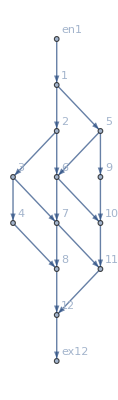

```mathematica
rulesgrid["FG"]/.rulesgrid["AssoCritical"]
```